```mathematica
d[k_]:=Flatten@ToExpression@StringSplit[Import["./BENCHMARK"][[k]],","];
l = (Length[Import["./BENCHMARK"]]-1)/2;
```

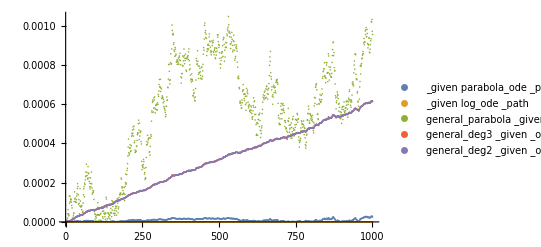

```mathematica
ListPlot[Table[Abs[(d[2k+1]-d[5])/d[5]],{k,1,5}],PlotLegends->Table[d[2*k][[1]],{k,1,5}]]
```

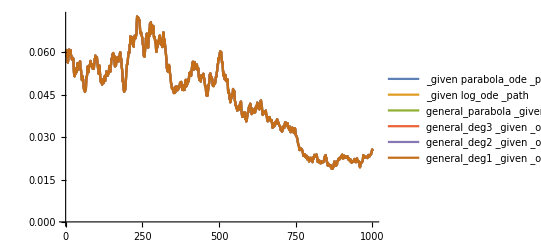

```mathematica
ListLinePlot[Table[d[2*k+1],{k,1,l}],PlotLegends->Table[d[2*k][[1]],{k,1,l}],PlotRange->Full]
```